## Virtual Device and questlink

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

```mathematica
Get["../vqd.wl"]
```

```mathematica
Options[SiliconDelft]={
qubitsNum->6,
(*average of T1*)
T1->10^5,
(* T2^* : Implementation might be incorrect *)
T2s-><|0->3,1-> 2.5,2-> 3.7,3-> 3.7,4-> 5.9,5-> 5.1|>,
(* T2 obtained by echo RX[π/2]-τ-RX[π]-τ-RX[π/2], where τ=1μs *)
T2-><|0->14,1-> 21.1,2-> 40.1,3-> 37.2,4-> 44.7,5-> 26.7|>,
(* If true, then the noise model uses T2s otherwise T2 *)
DDActive->True,
(* EDIT: Qubit frequency of each qubit in MHz *)
QubitFreq-><|0->15.62*10^3,1-> 15.88*10^3,2-> 16.3*10^3,3-> 16.1*10^3,4-> 15.9*10^3,5-> 15.69*10^3|>,
(*rabi frequencies on single rotations: 5 is average *)
RabiFreq-><|0->5,1->5,2->5,3->5,4->5,5->5|>,
(* Set the noise form of off-resonant Rabi oscillation. This takes RabiFreq information to produce the noise.*)
OffResonantRabi->True,

(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->True,

(* Fidelities of X- and Y- rotations by random benchmarking *)
FidSingleXY-><|0->0.9977,1-> 0.9987,2-> 0.9996,3-> 0.9988,4-> 0.9991,5-> 0.9989|>,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingleXY->{0,1},
(*  The rabi Frequency (MHz) and fidelities of controlled-Z, C[Z], nearest-neighbors, where the control qubits are the lower one. Keys are the control qubits *)
FreqCZ-><|0->12.1,1-> 11.1,2-> 6.6,3-> 9.8,4-> 5.4|>,
(* obtained from a simple optimisation via bell state fidelity *)
FidCZ-><|0->0.9526707113340579,1->0.9395929490898237,2->0.9484194291327452,3->0.9850519102118337,4->0.9663173858117854|>,
(* Error fraction/ratio {depolarising, dephasing} of controled-Rz rotation *)
EFCZ->{0,1},
(* Crosstalks error (C-Rz[ex])on the passive qubits when applying CZ gates;square matrix with dims nqubit-2
*)
ExchangeRotOn->{{0,0.023, 0.018 ,0.03, 0.04},{0.05 ,0,0.03, 0.03, 0.04},{0.05, 0.03 ,0,0.07, 0.042},{0.038 ,0.03 ,0.031,0 ,0.25},{0.033, 0.03 ,0.02, 0.03,0}},
(* Crosstalks error (C-Rz[ex])on the passive qubits when no CZ gates applied *)
ExchangeRotOff-><|0->0.039,1-> 0.015 ,2->0.03 ,3->0.02,4-> 0.028|>,

(* Single readout fidelity and duration of the edge qubits, ie 01 and 56 *)
FidRead->0.99,
DurRead->10,
RepeatRead->2
};
```

## Simple noise parameters optimisation in VQD

```mathematica
ClearAll[GradDescent]
SetAttributes[GradDescent,HoldAll]
GradDescent[params_,objf_,conf_]:=Module[{cost,basecost,grad,paramst,paramst2},
basecost=objf[params];
grad=Table[
paramst=params;
paramst2=params;
paramst[k]=N[paramst[k]+conf["dθ"]];
paramst2[k]=N[paramst[k]-conf["dθ"]];
N[(objf[paramst]-objf[paramst2])*0.5/conf["dθ"] ]
,{k,Keys@params}]
]

SetAttributes[UpdateCost,HoldAll]
UpdateCost[params_,objf_,conf_]:=Module[{grad, beststep,gradstep,tparams,cbest,cnew},
beststep=conf["gradstep"];
gradstep=beststep;
grad=GradDescent[params,objf,conf];

tparams=Normal@params;
tparams[[All,2]]-=conf["gradstep"]*grad;
cbest=objf[tparams];
If[NumberQ[conf["gradstepmultiply"]],

While[True,
gradstep*=conf["gradstepmultiply"];
tparams=Normal@params;
tparams[[All,2]]-=gradstep*grad;
cnew=objf[tparams];

If[cnew>=cbest, Break[]];
cbest=cnew;
beststep=gradstep
];
];
tparams=Normal@params;
tparams[[All,2]]-=beststep*grad;
params=Association@tparams;
cbest
]

ParamsFit::usage="ParamsFit[device, conf]. Parameterisation fitting.";
SetAttributes[ParamsFit,HoldAll]
ParamsFit[params_,objf_,conf_]:=Module[{cost, iter,dcost,oldcost,oldparams,paramsinit,initgradstep=conf["gradstep"],converge=0,costlist={},costinit,fail=0,maxfail=10,msg=""},
iter=0;
cost=objf[params];
costinit=cost;paramsinit=params;
AppendTo[costlist,cost];
Monitor[
While[True,
oldcost=cost;
oldparams=params;
cost=UpdateCost[params,objf,conf];

dcost=cost-oldcost;
If[dcost>=0&&iter>1,
(*revert to old cond*)
{cost,params}={oldcost,oldparams};
fail++;
conf["gradstep"]*=0.5;
msg="fail "<>ToString[fail]<>" times due to increasing cost. Set gradstep to "<>ToString[conf["gradstep"],FortranForm];
If[fail>=maxfail, (*consecutive maxfails*)
Print["Reach consecutive maxfails. Optimisation fails"];
Break[];
]
,
fail=0;
conf["gradstep"]=initgradstep;
msg="Recovered from fail. Set gradstep to "<>ToString[conf["gradstep"],FortranForm];
];

If[cost<=conf["costfin"],
Print["seems converged to dcost=",dcost];
Break[]
];

If[(++iter> conf["maxiter"])||converge>=conf["convergenum"],
Print["Reach maxiter or too flat: dcost=",dcost];
Break[]];

AppendTo[costlist,cost];
];
,Column@{"cost="<>ToString@cost,"iter="<>ToString@iter,msg}];

If[cost>=costinit,
Print["Optimisation have failed, use the initial parameter guess"];
{cost,params}={costinit,paramsinit}
];

AppendTo[costlist,cost];
Print[ListPlot[costlist]];
{objf[params],params}
]
```

## Fitting the Bell state

```mathematica
(* a set of random initial states 
It doesn't work for a set. Cannot handle shot noise?
*)
ρmat=Table[RandomMixState[6],{1}];
```

```mathematica
bellcircρ=<|"01"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"12"->{Subscript[Rx, 1][π/2],Subscript[Rx, 2][π/2],Subscript[C, 1][Subscript[Z, 2]],Subscript[Rx, 2][π/2]},"23"->{Subscript[Rx, 2][π/2],Subscript[Rx, 3][π/2],Subscript[C, 2][Subscript[Z, 3]],Subscript[Rx, 3][π/2]},"34"->{Subscript[Rx, 3][π/2],Subscript[Rx, 4][π/2],Subscript[C, 3][Subscript[Z, 4]],Subscript[Rx, 4][π/2]},"45"->{Subscript[Rx, 4][π/2],Subscript[Rx, 5][π/2],Subscript[C, 4][Subscript[Z, 5]],Subscript[Rx, 5][π/2]}|>;
bellcircψ=<|"01"->{Subscript[X, 0],Subscript[Rx, 0][π/2],Subscript[Rx, 1][-π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"12"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"23"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"34"->{Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]},"45"->{Subscript[X, 1],Subscript[Rx, 0][π/2],Subscript[Rx, 1][π/2],Subscript[C, 0][Subscript[Z, 1]],Subscript[Rx, 1][π/2]}|>;
```

```mathematica
ρ=CreateDensityQureg[6];
ρ2=CreateDensityQureg[2];
ψ=CreateQureg[6];
ψ2=CreateQureg[2];
```

```mathematica
concurence[ρ_]:=Module[{eigv,ρm,ρms,ρt,nq,pauliy},
ρm=GetQuregMatrix@ρ;
nq=IntegerPart@Log2@Length@ρm;
ρms=MatrixPower[ρm,1/2];
pauliy=CalcCircuitMatrix[Subscript[Y, #]&/@Range[0,nq-1]];
ρt=pauliy.Conjugate[ρm].pauliy;
eigv=Reverse@Sort[Chop@Eigenvalues[MatrixPower[ρms.ρt.ρms,1/2]]];
Max[0,eigv[[1]]-Total@eigv[[2;;]]]
]


bellcost[params_]:=Module[{init,qubits,plot,codes,fidtarget,conctarget,opt,noisycirc},
codes=ReplaceList[Sort@Range[0,5],{p___,a_,b_,q___}:>StringRiffle[{a,b},""]];
fidtarget=<|"01"->89.2,"12"->90.1,"23"->88.3,"34"->95.6,"45"->94.1|>;
conctarget=<|"01"->86.7,"12"->83.9,"23"->87.9,"34"->94.9,"45"->90.6|>;
opt={FidCZ-><|0->Subscript[θ, 0],1->Subscript[θ, 1],2->Subscript[θ, 2],3->Subscript[θ, 3],4->Subscript[θ, 4]|>}/.params;
Mean@Table[
init={};
qubits=ToExpression@StringSplit[code,""];
If[Length@Intersection[qubits,{0,1,2}]>0,AppendTo[init,{Subscript[Init, 0,1,2],Subscript[Init, 0,1,2]}]];
If[Length@Intersection[qubits,{3,4,5}]>0,AppendTo[init,{Subscript[Init, 3,4,5],Subscript[Init, 3,4,5]}]];
SetQuregMatrix[ρ,RandomChoice[ρmat]];
noisycirc=ExtractCircuit@InsertCircuitNoise[Serialize@{init,bellcircρ[code]},SiliconDelft[Sequence@@opt], ReplaceAliases->True];
noisycirc=SimplifyCircuit[DeleteCases[DeleteCases[noisycirc,Subscript[Depol, __][0.]],Subscript[Deph, __][0.]]];
ApplyCircuit[ρ,noisycirc];
SetQuregMatrix[ρ2,PartialTrace[ρ,Sequence@@Complement[Range[0,5],qubits]]];
ApplyCircuit[InitZeroState@ψ2,bellcircψ[code]];
Abs[CalcFidelity[ρ2,ψ2]*100-fidtarget[code]]+0.5*Abs[concurence[ρ2]*100-conctarget[code]]
,{code,codes}]
]
```

```mathematica
SetAttributes[shock,HoldFirst]
shock[params_,dθ_]:=Module[{rands},
Table[
rands=RandomChoice[{-1,1}]*dθ;
If[(params[k]+rands)>=1,
params[k]+=rands,
params[k]-=rands
]
,{k,Keys@params}]
]
```

```mathematica
params=<|Subscript[θ, 0]->0.95,Subscript[θ, 1]->0.94,Subscript[θ, 2]->0.935,Subscript[θ, 3]->0.96,Subscript[θ, 4]->0.97|>;
```

```mathematica
rfid=RandomVariate[NormalDistribution[0.91,0.01],5]
idx=0;
params=Association[(Subscript[θ, idx++]->#&/@rfid)]
```

{0.920391,0.915213,0.911049,0.918051,0.910486}

<|θ_0→0.920391,θ_1→0.915213,θ_2→0.911049,θ_3→0.918051,θ_4→0.910486|>

Reach consecutive maxfails. Optimisation fails

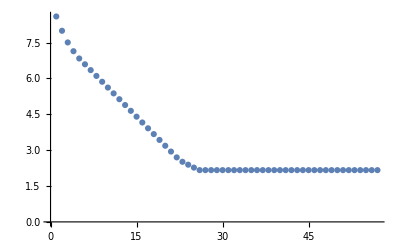

```mathematica
confinit=<|
"nqubits"->6,
"maxiter"->1000,
"gradstep"->10^-4,
"gradstepmultiply"->False,
(* delta params *)
"dθ"->10^-6,
"convergenum"->10,
"costfin"->10^-8
|>;

conf=confinit;
{cost,params}=ParamsFit[params,bellcost,conf];
```

```mathematica
cost
```

2.16498

```mathematica
i=0;
Association[i++->#&/@Values@params]
```

<|0→0.923184,1→0.92518,2→0.916554,3→0.979886,4→0.965077|>

```mathematica
bellcost[params]
```

2.16498

```mathematica
fids[params_]:=Module[{init,qubits,plot,codes,fidtarget,opt,dev,noisycirc},
codes=ReplaceList[Sort@Range[0,5],{p___,a_,b_,q___}:>StringRiffle[{a,b},""]];
opt={FidCZ-><|0->Subscript[θ, 0],1->Subscript[θ, 1],2->Subscript[θ, 2],3->Subscript[θ, 3],4->Subscript[θ, 4]|>}/.params;
dev=SiliconDelft[Sequence@@opt];
Table[
init={};
qubits=ToExpression@StringSplit[code,""];
If[Length@Intersection[qubits,{0,1,2}]>0,AppendTo[init,Subscript[Init, 0,1,2]]];
If[Length@Intersection[qubits,{3,4,5}]>0,AppendTo[init,Subscript[Init, 3,4,5]]];
SetQuregMatrix[ρ,RandomChoice@ρmat];
noisycirc=ExtractCircuit@InsertCircuitNoise[Serialize@{init,bellcircρ[code]},SiliconDelft[Sequence@@opt], ReplaceAliases->True];
noisycirc=SimplifyCircuit[DeleteCases[DeleteCases[noisycirc,Subscript[Depol, __][0.]],Subscript[Deph, __][0.]]];
ApplyCircuit[ρ,noisycirc];
SetQuregMatrix[ρ2,PartialTrace[ρ,Sequence@@Complement[Range[0,5],qubits]]];
ApplyCircuit[InitZeroState@ψ2,bellcircψ[code]];
{CalcFidelity[ρ2,ψ2]*100,concurence[ρ2]*100}
,{code,codes}]
]
```

```mathematica
fids[params]
```

{{88.8553,78.6932},{89.8395,79.7478},{88.3939,78.5},{95.2082,93.2733},{93.8377,89.6589}}